```mathematica
Remove["Global`*"]
```

A Projectile is fired with initial speed v0 and at an angle a with respect to the horizontal. Its range is given by R. Plot R as a function of a

```mathematica
v0 = 30; (* Initial speed m/sec*)
g = 9.8; (* Acceleration due to gravity m/sec^2*)
```

```mathematica
R = 2v0^2 Cos[a] Sin[a]/g (* Range of projectile*)
```

183.673 Cos[a] Sin[a]

0

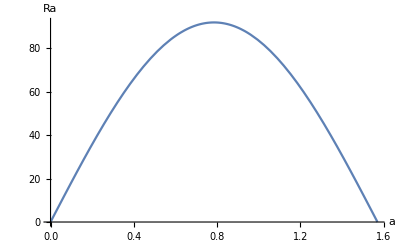

```mathematica
amin = 0
amax = Pi/2;
Plot[R,{a,amin,amax}, PlotLegends->"Range", AxesLabel->{a, Ra}]
```